```mathematica
p0 = {{x0},y0,0};
p1= {{x1},y1,0};
p2={{x2},y2,0};
iparg = {p0,p1,p2};
plotrules = {
x0->0.0,y0->0.0,
x1->1.0,y1->1.0,
x2->2.0,y2->0.5};

InterpolatingPolynomial[iparg/.plotrules,x]
```

0.5+(-2+x)^2 (-0.125+x (-0.125+(0.75-0.375 (-1+x)) x))

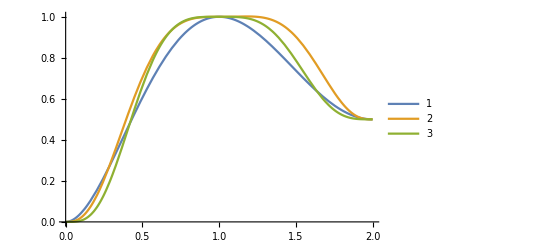

```mathematica
howmany=2;
manyargs = Table[Map[Nest[Append[#,0]&,#,i]&,iparg],{i,0,howmany}];
funcs =Map[InterpolatingPolynomial[#/.plotrules,x]&,manyargs];
Plot[funcs,{x,0,2},PlotLegends->LineLegend[Automatic]]
```

Interpolating Polynomial of more points yields numerical instability: 
5 points 
and 
6 derivatives equal to 0.

```mathematica
howmany = 5; (*Number of points*)
Xpts =Array[#&,howmany,{0,howmany-1}];
XYpts = Map[#/.{arg_->{arg,RandomReal[]}}&,Xpts];
(*XYptsRational = Map[#/.{arg_->{arg,Rationalize[RandomReal[],0]}}&,Xpts];*)
```

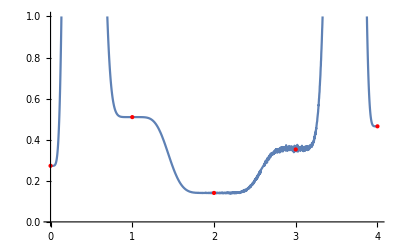

```mathematica
diffs = 6;(*Number of differentials equal 0 at points*)
InterPolylist = Map [#/.{{x_,y_}->Join[
{{x},y},
If[diffs>0,Table[0,{j,1,diffs}],{}]
]
}&,XYpts];
fun = FullSimplify[InterpolatingPolynomial[InterPolylist ,x]];

Show[{
Plot[fun,{x,0,howmany-1 },
(*PlotPoints->4,
Mesh->All,
MaxRecursion->2,*)
PlotRange->{0,1},
PlotLegends->LineLegend[Automatic]
],
ListPlot[XYpts,PlotStyle->{Red,PointSize[Large]}]
}]
```